```mathematica
nudata=Import[NotebookDirectory[]<>"nudata.dat"];
```

```mathematica
xmin=0;
xmax=50;
nbins=20;
xrange=N[Table[xmin+i*(xmax)/nbins,{i,0,nbins}]]
```

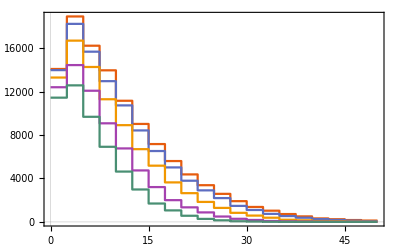

```mathematica
imhnl=1;
nutable={};
Do[
nutable0=Table[{xrange[[i]],nudata[[l,2+i]]},{i,1,20}];
AppendTo[nutable,nutable0];
,{l,imhnl,imhnl+4}]
ListStepPlot[nutable,PlotTheme->"Scientific"]
```

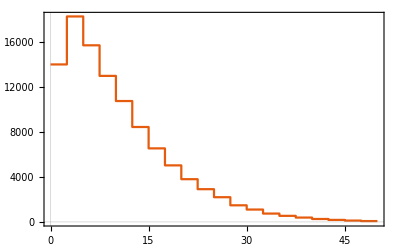

```mathematica
imhnl=1;
ioffaxis=2;
nutable={};
nutable0=Table[{xrange[[i]],nudata[[(imhnl-1)*5+ioffaxis,2+i]]},{i,1,20}];
AppendTo[nutable,nutable0];
ListStepPlot[nutable,PlotTheme->"Scientific"]
```

```mathematica
nutable={}
```

```mathematica
nutable={};
Do[
auxtable={};
Do[
AppendTo[auxtable,Table[{xrange[[l]],nudata[[j,2+l]]},{l,1,20}]];
,{j,(i-1)*5+1,(i-1)*5+1+4}];
AppendTo[nutable,auxtable];
,{i,1,4}]
```

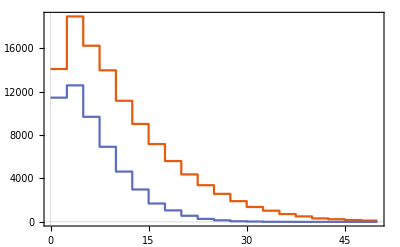

```mathematica
ListStepPlot[{nutable[[1,1]],nutable[[1,5]]},PlotTheme->"Scientific"]
```